## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170818";

(*键名直接用短名，里面加上下划线*)
inspiralParams={};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

Part::partw: Part 5 of Missing[KeyAbsent,dphi_0] does not exist.

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00081};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1.5]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 19087 + 镜像 19087

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.57839×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.57839×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.00081}，共 2 条

第一条前3点：{{35.2306,34.5671},{35.2306,34.5666},{35.3881,34.4263}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.769017

可信水平百分比：76.9017%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.769017

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
m1m2PDF[p][42,28]
```

0.00303946

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

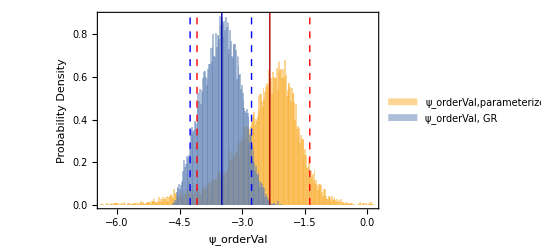

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.115492, 0.884508}

实际使用的 GR 概率区间上下界: {-4.06714, -2.94591}

实际使用的 Param 概率区间上下界: {-3.4314, -1.63947}

GR下界: 点数=350 | Y>0点数=350 | 平均误差=0.432306

GR上界: 点数=350 | Y>0点数=350 | 平均误差=5.10068×10^-16

Param下界: 点数=350 | Y>0点数=350 | 平均误差=8.08242×10^-16

Param上界: 点数=350 | Y>0点数=350 | 平均误差=4.28863×10^-16

{{10.2,23.4382},{10.4,23.8978},{10.6,24.3574},{10.8,24.817},{11.,25.2765}}

{{10.2,214.332},{10.4,218.535},{10.6,222.738},{10.8,226.94},{11.,231.143}}

chi1L取值：0.750198

chi2L取值：0.522934

=====================================================

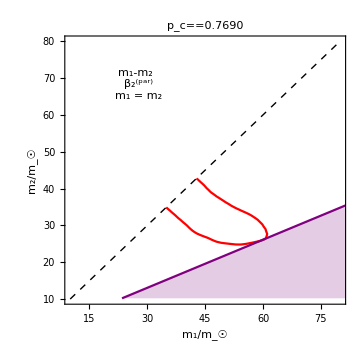

```mathematica
probability=prob;
(*probability=0.9999;*)

plots[p]=PlotInversion[p,probability,10,80,0.2,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00081};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 20890 + 镜像 20890

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.13311×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.13311×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.00081}，共 2 条

第一条前3点：{{34.8183,35.4823},{34.6918,35.5931},{34.5365,35.7511}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.819211

可信水平百分比：81.9211%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.819211

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

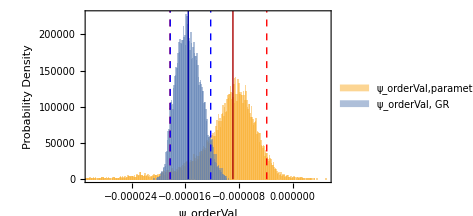

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.09035, 0.90965}

实际使用的 GR 概率区间上下界: {-0.0000178602, -0.0000128609}

实际使用的 Param 概率区间上下界: {-0.000015558, -4.8165×10^-6}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=9.48677×10^-23

Greater::nord: Invalid comparison with 15.1999+0.0464093 ⅈ attempted.

Greater::nord: Invalid comparison with 15.3999+0.0473659 ⅈ attempted.

Greater::nord: Invalid comparison with 15.5999+0.0483509 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR上界: 点数=250 | Y>0点数=0 | 平均误差=2.69487×10^-6

Param下界: 点数=250 | Y>0点数=250 | 平均误差=5.07949×10^-20

Param上界: 点数=2 | Y>0点数=2 | 平均误差=0.0000107393

{{15.2,15.146},{15.4,15.3453},{15.6,15.5446},{15.8,15.7439},{16.,15.9432}}

Part::take: Cannot take positions 1 through 5 in {{1,1},{100,100}}.

{{1,1},{100,100}}⟦1;;5⟧

chi1L取值：0.71309

chi2L取值：0.533405

=====================================================

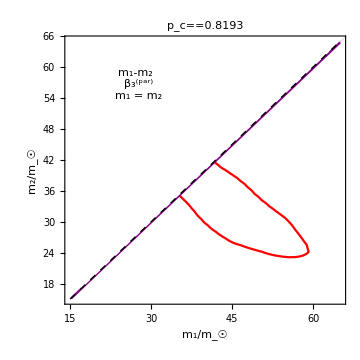

```mathematica
probability=prob;
probability=0.8193;
(*probability=0.82;*)

(* 蓝色要对称一下 *)
plots[p]=PlotInversion[p,probability,15,65,0.2,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},lineup->{{1,1},{100,100}},upStyle->None]
(*lineup->{{60,40},{1,1},{1,1},{1,1},{100,100}}*)
```

## Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,60},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0048675};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,60}

输入q范围：{1,3}

m1范围：{11.487,122.86}

m2范围：{6.82558,68.9219}

对称数据：原始 22557 + 镜像 22557

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.4063×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.4063×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 122.86} × {6.82558, 122.86}

等高线值：{0.0048675}，共 2 条

第一条前3点：{{36.9957,37.3583},{36.9785,37.3829},{36.9446,37.4313}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.0640605

可信水平百分比：6.40605%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.0640605

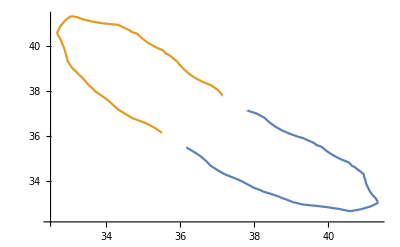

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

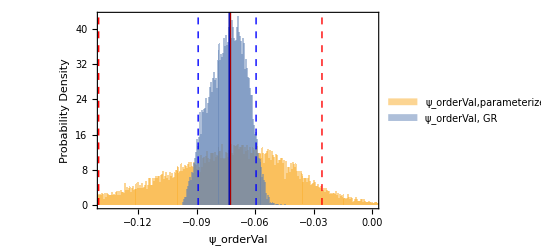

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.46797, 0.53203}

实际使用的 GR 概率区间上下界: {-0.0741338, -0.0724822}

实际使用的 Param 概率区间上下界: {-0.0753678, -0.0700682}

GR下界: 点数=150 | 平均误差=2.10017×10^-17

GR上界: 点数=150 | 平均误差=1.82262×10^-17

Param下界: 点数=150 | 平均误差=2.17419×10^-17

Param上界: 点数=150 | 平均误差=1.97065×10^-17

chi1L取值：0.596078

chi2L取值：0.546751

=====================================================

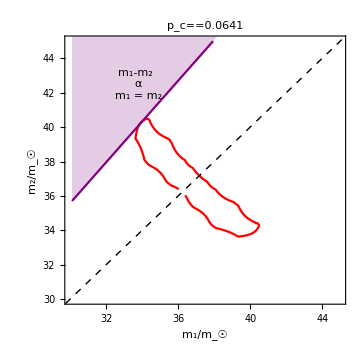

```mathematica
probability=prob;
(*probability=0.05;*)

PlotInversion[p,probability,30,45,0.1,cm->True,cd->False,cu->False,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0015};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.787888

可信水平百分比：78.7888%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.787888

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 20737 + 镜像 20737

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.8126×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.8126×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.0015}，共 2 条

第一条前3点：{{39.2083,39.8723},{39.1473,39.9515},{39.0873,40.0292}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.702955

可信水平百分比：70.2955%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.702955

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

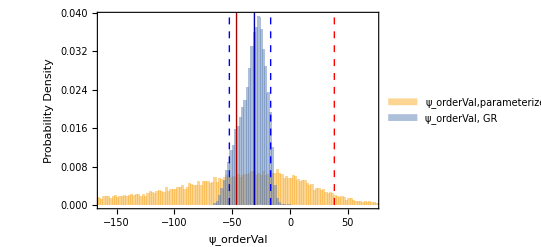

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.43075, 0.56925}

实际使用的 GR 概率区间上下界: {-32.826, -28.9965}

实际使用的 Param 概率区间上下界: {-58.2163, -35.0907}

GR下界: 点数=900 | 平均误差=2.14821×10^-14

GR上界: 点数=900 | 平均误差=2.11979×10^-14

Param下界: 点数=900 | 平均误差=23.1202

Param上界: 点数=900 | 平均误差=2.1111×10^-14

chi1L取值：0.633061

chi2L取值：0.562445

=====================================================

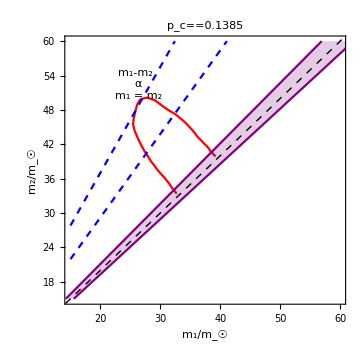

```mathematica
probability=prob;
probability=0.1385;

PlotInversion[p,probability,15,60,0.05,cm->True,cd->True,cu->True,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 22776 + 镜像 22776

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.50548×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.50548×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001}，共 2 条

第一条前3点：{{40.5447,39.8808},{40.5448,39.8808},{40.5514,39.874}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.855147

可信水平百分比：85.5147%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.855147

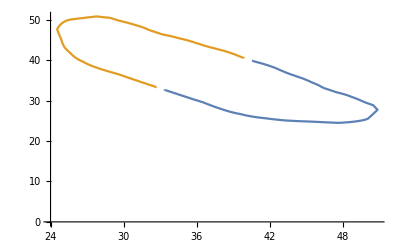

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

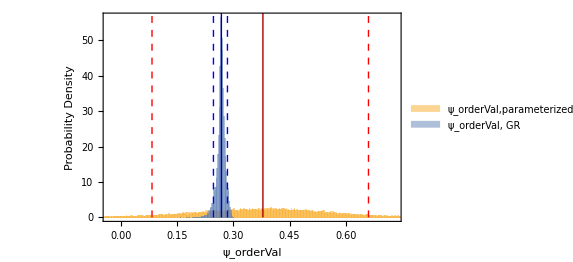

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.27375, 0.72625}

实际使用的 GR 概率区间上下界: {0.26322, 0.272847}

实际使用的 Param 概率区间上下界: {0.273953, 0.482231}

GR下界: 点数=400 | 平均误差=6.245×10^-17

GR上界: 点数=400 | 平均误差=4.42701×10^-17

Param下界: 点数=400 | 平均误差=2.38698×10^-17

Param上界: 点数=400 | 平均误差=0.208198

chi1L取值：0.666429

chi2L取值：0.51277

=====================================================

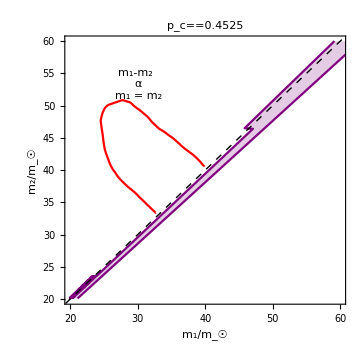

```mathematica
probability=prob;
probability=0.4525;

PlotInversion[p,probability,20,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

# utils

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

正在导出矢量图: plot_dbeta_3.pdf ...

正在导出矢量图: plot_dbeta_2.pdf ...